Ph. 20 Assignment 6
Grant Messner

1)

```mathematica
Clear[g,v]
```

```mathematica
V0[theta_,v_]:={v*Cos[theta],v*Sin[theta]}
```

```mathematica
r[theta_,v_,x_,y_,t_]:={x+V0[theta,v][[1]]*t,y+V0[theta,v][[2]]*t-(1/2)*g*t^2}
```

```mathematica
Solve[r[theta,v,0,0,t][[2]]==0,t]
```

{{t→0},{t→(2 v Sin[theta])/g}}

```mathematica
T=(2 v Sin[theta])/g
```

(2 v Sin[theta])/g

```mathematica
r[theta,v,0,0,T][[1]]
```

(2 v^2 Cos[theta] Sin[theta])/g

```mathematica
(2 v^2 Cos[theta] Sin[theta])/g
```

(2 v^2 Cos[theta] Sin[theta])/g

```mathematica
Simplify[(2 v^2 Cos[theta] Sin[theta])/g]
```

(v^2 Sin[2 theta])/g

```mathematica
Maximize[Sin[2theta],theta]
```

{1,{theta→π/4}}

```mathematica
Clear[v]
Solve[v^2*Sin[2*45 Degree]/(9.8)==1000,v]
```

{{v→-98.9949},{v→98.9949}}

So the optimal firing angle for a launch with starting height y = 0 is Pi/4, or 45 degrees. An initial velocity of about 99 m/s in maginitude is required to reach PCC in the absence of air drag, assuming the grapefruit is launched at the optimal angle of 45 degrees.

2)

```mathematica
g=9.8
```

9.8

```mathematica
ClearAll[t]
```

```mathematica
eqs={x''[t] ==0, y''[t]==-g}
```

{x''[t]==0,y''[t]==-9.8}

```mathematica
Clear[ini,vi,theta]
ini[vi_,theta_]:={x[0]==0,y[0]==0,x'[0]==vi*Cos[theta],y'[0]==vi*Sin[theta]}
```

```mathematica
Clear[rules,ti,tf]
rules[vi_,theta_,ti_,tf_]:=NDSolve[Join[eqs,ini[vi,theta]],{x,y},{t,ti,tf}]
```

```mathematica
ClearAll[x,y,xx,yy]
xx[vi_,theta_,ti_,tf_]:=x/.rules[vi,theta,ti,tf][[1]]
yy[vi_,theta_,ti_,tf_]:=y/.rules[vi,theta,ti,tf][[1]]
```

InterpolatingFunction[{{0., 3.}}, <>]

InterpolatingFunction[{{0., 3.}}, <>]

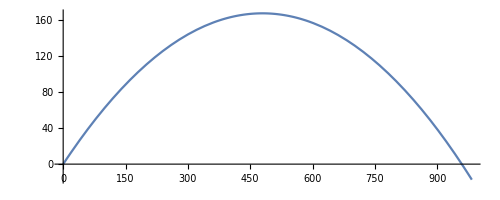

```mathematica
x1 =xx[100,35 Degree,0,3]
y1= yy[100,35 Degree,0,3]
P35 = ParametricPlot[{x1[t],y1[t]},{t,0,12}]
```

InterpolatingFunction[{{0., 3.}}, <>]

InterpolatingFunction[{{0., 3.}}, <>]

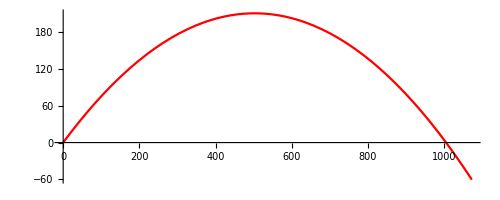

```mathematica
x2=xx[100,40 Degree,0,3]
y2= yy[100,40 Degree,0,3]
P40 = ParametricPlot[{x2[t],y2[t]},{t,0,14},PlotStyle->Red]
```

InterpolatingFunction[{{0., 3.}}, <>]

InterpolatingFunction[{{0., 3.}}, <>]

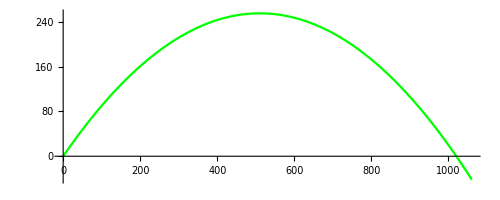

```mathematica
x3=xx[100,45 Degree,0,3]
y3= yy[100,45 Degree,0,3]
P45= ParametricPlot[{x3[t],y3[t]},{t,0,15},PlotStyle->Green]
```

InterpolatingFunction[{{0., 3.}}, <>]

InterpolatingFunction[{{0., 3.}}, <>]

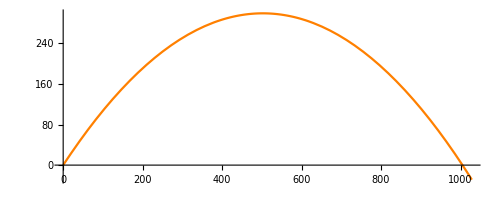

```mathematica
x4=xx[100,50 Degree,0,3]
y4= yy[100,50 Degree,0,3]
P50= ParametricPlot[{x4[t],y4[t]},{t,0,16},PlotStyle->Orange]
```

InterpolatingFunction[{{0., 3.}}, <>]

InterpolatingFunction[{{0., 3.}}, <>]

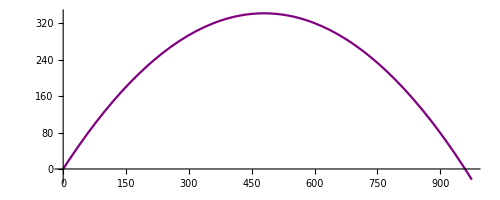

```mathematica
x5=xx[100,55 Degree,0,3]
y5= yy[100,55Degree,0,3]
P55= ParametricPlot[{x5[t],y5[t]},{t,0,17},PlotStyle->Purple]
```

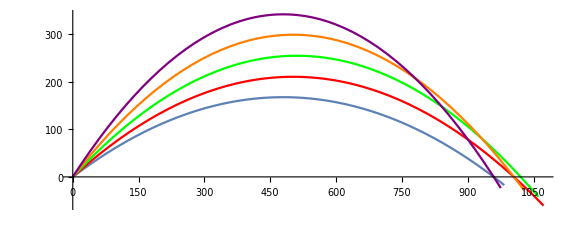

```mathematica
Show[P35,P40,P45,P50,P55,PlotRange->All,ImageSize->Large]
```

The colors each correspond to a particular launch angle with a fixed initial velocity of 100 m/s. The correspondences are blue -> 35 degrees, red -> 40 degrees, green -> 45 degrees, orange -> 50 degrees, purple -> 55 degrees. As we can see from the plot, the green 45 degree trajectory is optimal if we do not take air drag into account.

3)

```mathematica
AccDragCoeff[rho_,r_,m_]:=(1/(2*m))*rho*r^2
```

```mathematica
ClearAll[eqs2,t]
eqs2={x''[t] ==-AccDragCoeff[1.3,.05,.5]*x'[t]*(Sqrt[x'[t]^2+y'[t]^2]), y''[t]==-AccDragCoeff[1.3,.05,.5]*y'[t]*(Sqrt[x'[t]^2+y'[t]^2])-g}
```

{x''[t]==-0.00325 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8-0.00325 y'[t] √(x'[t]^2+y'[t]^2)}

```mathematica
Clear[ini2,vi,theta]
ini2[vi_,theta_]:={x[0]==0,y[0]==0,x'[0]==vi*Cos[theta],y'[0]==vi*Sin[theta]}
```

```mathematica
Clear[rules2,ti,tf]
rules2[vi_,theta_,ti_,tf_]:=NDSolve[Join[eqs2,ini2[vi,theta]],{x,y},{t,ti,tf}]
```

```mathematica
ClearAll[x,y,xx2,yy2]
xx2[vi_,theta_,ti_,tf_]:=x/.rules2[vi,theta,ti,tf][[1]]
yy2[vi_,theta_,ti_,tf_]:=y/.rules2[vi,theta,ti,tf][[1]]
```

InterpolatingFunction[{{0., 15.}}, <>]

InterpolatingFunction[{{0., 15.}}, <>]

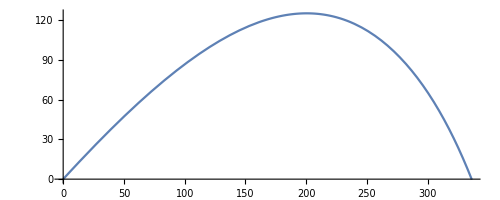

```mathematica
x12 =xx2[100,45 Degree,0,15]
y12= yy2[100,45 Degree,0,15]
P452 = ParametricPlot[{x12[t],y12[t]},{t,0,10}]
```

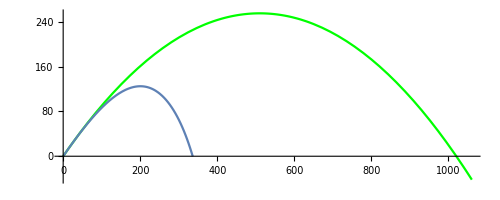

```mathematica
Show[P45,P452]
```

The above plot show the trajectories of the projectile launched at 100 m/s with launch angle of 45 degrees with (blue) and without (green) air drag taken into account in the equations of motion. As we can see from the plot, the grapefruit travels approximately 700 m farther with no air resistance!

4)

InterpolatingFunction[{{0., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

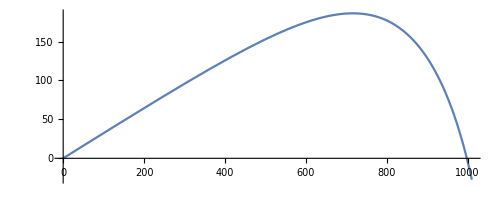

```mathematica
x13 =xx2[790,18Degree,0,20]
y13= yy2[790,18Degree,0,20]
P18 = ParametricPlot[{x13[t],y13[t]},{t,0,12}]
```

InterpolatingFunction[{{0., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

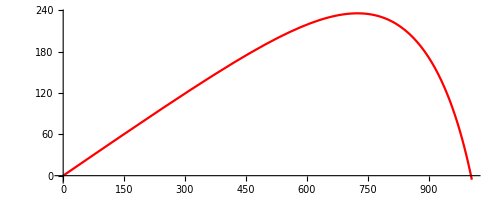

```mathematica
x23 =xx2[780,22Degree,0,20]
y23= yy2[780,22Degree,0,20]
P22 = ParametricPlot[{x23[t],y23[t]},{t,0,13},PlotStyle->Red]
```

InterpolatingFunction[{{0., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

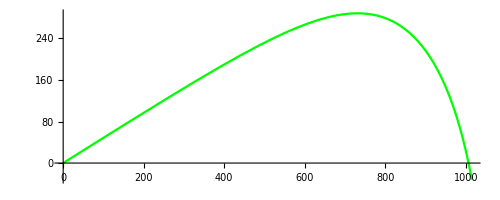

```mathematica
x33 =xx2[790,26Degree,0,20]
y33= yy2[790,26Degree,0,20]
P26 = ParametricPlot[{x33[t],y33[t]},{t,0,15},PlotStyle->Green]
```

InterpolatingFunction[{{0., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

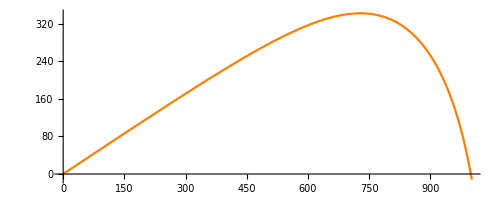

```mathematica
x43 =xx2[800,30Degree,0,20]
y43= yy2[800,30Degree,0,20]
P30 = ParametricPlot[{x43[t],y43[t]},{t,0,16},PlotStyle->Orange]
```

InterpolatingFunction[{{0., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

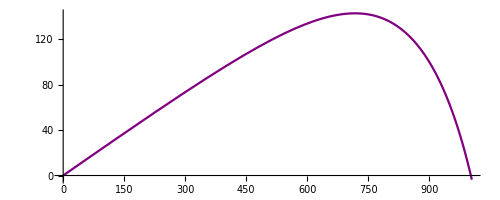

```mathematica
x53 =xx2[860,14Degree,0,20]
y53= yy2[860,14Degree,0,20]
P14 = ParametricPlot[{x53[t],y53[t]},{t,0,10},PlotStyle->Purple]
```

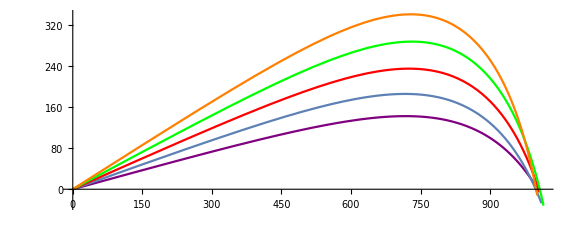

```mathematica
Show[P14,P18,P22,P26,P30,PlotRange->All,ImageSize->Large]
```

Comparison of different trajectories (i.e., different launch angle and initial velocity) required to reach a distance of ~1000 m. The corresponding trajectories are: purple -> 14 degree launch angle, 860 m/s initial velocity, blue -> 18 degree launch angle, 790 m/s initial velocity, red -> 22 degree launch angle, 780 m/s initial velocity, green -> 26 degree launch angle, 790 m/s initial velocity, orange  -> 30 degree launch angle, 860 m/s velocity. Thus, we can see that the red 22 degree trajectory is approximately the optimal one for this case.

5)
(a)

```mathematica
Needs["FunctionApproximations`"]
```

```mathematica
Clear[tau,T]
tau[vi_,theta_,ti_,tf_]:=T/.InterpolateRoot[yy2[vi,theta Degree,ti,tf][T]==0,{T,(tf - ti)/2,tf}]
```

The above tau function returns the approximate time tau at which the grapefruit hits the ground.

(b)

```mathematica
range[vi_,theta_,ti_,tf_]:=xx2[vi,theta Degree,ti,tf][Tau]/.Tau->tau[vi,theta,ti,tf]
```

The above range function returns the range of the projectile (i.e., how far it travels in the x direction before it hits the ground), as a function of the initial launch conditions.

(c)

```mathematica
VBest[theta_,ti_,tf_,v0_,vn_,nsteps_,xf_]:=
For[v = v0,v<vn,v=v+(vn - v0)/nsteps,
Module[{r = range[v,theta,ti,tf]},If[r>xf,
Return[N[v]],,Print[range[v,theta,ti,tf]
]]
]
]
```

The above function determines (to a given precision...specified by the number of steps nsteps) the minimum velocity required to reach a certain distance xf, given the usual initial conditions theta, ti, and tf, as well as a lower and upper bound v0 and vn on the velocity.

(d)

```mathematica
ThetaBest[ti_,tf_,v0_,vn_,thetamin_,thetamax_,nsteps_,xf_,n_]:=
Module[{min=thetamin,max=thetamax},For[i = 0,i<n,i++,
If[VBest[max,ti,tf,v0,vn,nsteps,xf]<VBest[min,ti,tf,v0,vn,nsteps,xf],
min=(min+max)/2,max=(min+max)/2,Print[min,max]]
];Return[N[(min+max)/2]]]
```

```mathematica
Print[ThetaBest[0,25,700,1100,20,40,100,1000,10]]
```

23.1348

The above function ThetaBest computes the “optimal” angle theta in the range (thetamin, thetamax), in the sense that this angle requires the lowest initial velocity to reach some distance xf. The function does this by performing a binary search with a depth of n. The parameters ti, tf, v0, vn, nsteps and passed into the function VBest. The optimal angle for our scenario is about 23.1 degrees, using the initial parameters above.